# Lagrangian Dynamics

```mathematica
Clear["'*"];
```

Consider a pendulum consisting of a mass attached to a massless spring, as shown below.

A is a constant equal to the location of the mass when the spring is unstretched.

x is positive downward.


How many degrees of freedom? Two. We will use x and θ as our generalized coordinates.

```mathematica
T=1/2 m(A+x)^2 θdot^2+1/2 m xdot^2;
U=-m g (A+x) Cos[θ]+1/2 k x^2;
L=T-U
```

-(k x^2)/2+(m xdot^2)/2+1/2 m (A+x)^2 θdot^2+g m (A+x) Cos[θ]

Now take derivatives with respect to everything and put in explicit time dependence while we're at it.

```mathematica
pθ=D[L,θdot]/.{θ->θ[t],x->x[t],θdot->θ'[t],xdot->x'[t]}
px=D[L,xdot]/.{θ->θ[t],x->x[t],θdot->θ'[t],xdot->x'[t]}
fθ=D[L,θ]/.{θ->θ[t],x->x[t],θdot->θ'[t],xdot->x'[t]}
fx=D[L,x]/.{θ->θ[t],x->x[t],θdot->θ'[t],xdot->x'[t]}
```

m (A+x[t])^2 θ'[t]

m x'[t]

-g m Sin[θ[t]] (A+x[t])

g m Cos[θ[t]]-k x[t]+m (A+x[t]) θ'[t]^2

Now create the differential equations.

```mathematica
θeq=D[pθ,t]==fθ
xeq=D[px,t]==fx
```

2 m (A+x[t]) x'[t] θ'[t]+m (A+x[t])^2 θ''[t]==-g m Sin[θ[t]] (A+x[t])

m x''[t]==g m Cos[θ[t]]-k x[t]+m (A+x[t]) θ'[t]^2

Define the variables, add initial conditions, and solve the equations.

```mathematica
m=0.2;
A=1.5;
g=9.8;
k=6;
sol1=NDSolve[{θeq,xeq,x[0]==0,θ[0]==π/6,x'[0]==0,θ'[0]==0},{x[t],θ[t]},{t,0,20}]
```

{{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

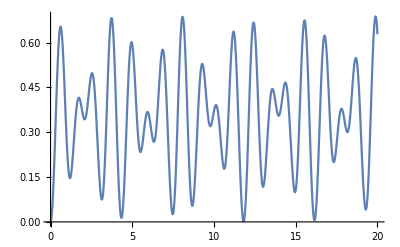

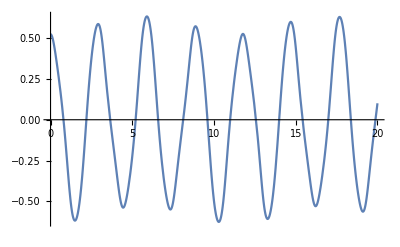

```mathematica
x[t_]=x[t]/.sol1[[1]];
θ[t_]=θ[t]/.sol1[[1]];
Plot[x[t],{t,0,20}]
Plot[θ[t],{t,0,20}]
```

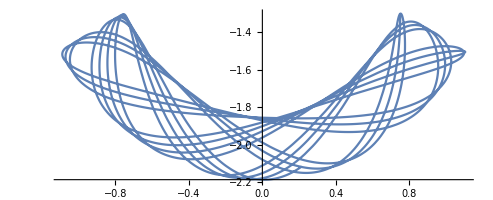

```mathematica
ParametricPlot[{(A+x[t])*Sin[θ[t]],-(A+x[t])*Cos[θ[t]]},{t,0,20}]
```